```mathematica
a = RandomVariate[BetaDistribution[1450+1, 8500-1450+1], 1000];
b = RandomVariate[BetaDistribution[1500+1, 8500-1500+1], 1000];
```

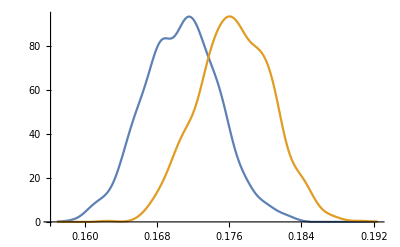

```mathematica
SmoothHistogram[{a,b}]
```

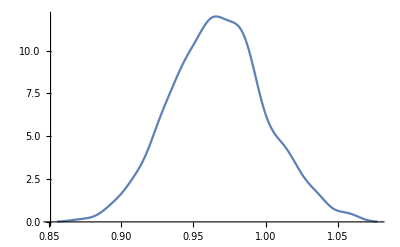

```mathematica
SmoothHistogram[a/b]
```

```mathematica
Quantile[a/b, {.025, .5, .975}]
```

{0.905138,0.966548,1.03473}

```mathematica
Quantile[a-b, {.025, .5, .975}]
```

{-0.0175594,-0.00585236,0.00594644}

```mathematica
TTest[{a, b}]
```

3.22456×10^-182

```mathematica
Mean[a]
Mean[b]
```

0.170687

0.176589

```mathematica
Total[
Negative[a-b]
]
```

152 False+848 True